```mathematica
Clear["Global`*"];
```

```mathematica
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
a=1;
b=100;
U[x_,y_]=(a-x)^2+b (y-x^2)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
QShmc=hmc[U,dU,ddU,2,2000,4000,True,False];
QSrhmc=hmc[U,dU,ddU,2,2000,4000,False,False];
QSchmc=hmc[U,dU,ddU,2,2000,4000,True,True];
```

501 1218.74 8.76351 0.526763 0.367241 17.0342 1235.77 1149.87 0.000567 0.0001 True {1,2,11} {1,11}

1002 473.761 5.214 0.612498 0.433565 9.5636 483.325 1149.87 0.00121542 0.0001 True {1,6,10,11} {1,11}

1503 233.854 5.2247 0.729495 0.377335 10.3414 244.195 1149.87 0.00110492 0.0001 True {1,2,7,11} {1,11}

2004 256.676 12.63 0.348506 0.34708 10.9421 267.618 1149.87 0.00121542 0.0001 True {1,2,3,6,11} {1,11}

2505 263.012 8.69262 0.546485 0.449082 4.60628 267.618 1149.87 0.00121542 0.0001 True {1,2,11} {1,11}

3006 261.608 5.8874 0.5865 0.456376 6.01014 267.618 1149.87 0.00121542 0.0001 True {1,2,5,6,7,11} {1,11}

3507 259.668 14.0799 0.703167 0.445539 7.95011 267.618 1149.87 0.00121542 0.0001 True {1,3,8,9,10} {1,8,10,11}

501 840.907 1.03952 0.390788 0.444342 15.7284 6145.86 856.635 1.×10^-9 0.0717952 False {1,10,11} {1,7,10,11}

1002 500.443 2.30366 0.541951 0.488976 12.864 6145.86 513.307 1.×10^-9 0.0717952 False {1,8,11} {1,3,5,11}

1503 484.189 0.716625 0.406377 0.365065 11.705 6145.86 495.894 1.×10^-9 0.0593349 False {1,5,11} {1,8,11}

2004 436.029 1.14609 0.351242 0.370394 15.5465 6145.86 451.576 1.×10^-9 0.0789747 False {1,4,11} {1,11}

2505 437.911 0.998152 0.584624 0.406148 13.6647 6145.86 451.576 1.×10^-9 0.0789747 False {1,11} {2,3,5,7,10,11}

3006 439.943 1.21897 0.498594 0.454532 11.6327 6145.86 451.576 1.×10^-9 0.0789747 False {1,11} {1,3,11}

3507 438.715 -5.75895 0.668819 0.374961 12.8611 6145.86 451.576 1.×10^-9 0.0789747 False {1,4,5,8,11} {1,2,7,11}

501 590.8 9.87316 0.519841 0.436669 8.92963 599.73 615.622 0.000425996 0.0156247 True {1,10,11} {1,11}

1002 481.121 -0.115908 0.303965 0.39827 12.0532 464.608 493.174 0.000567 0.0276801 False {1,2,4,6,11} {1,2,4,5,8,11}

1503 406.866 13.3468 0.558831 0.386195 11.5654 418.431 324.247 0.00068607 0.033493 True {1,3,10,11} {1,11}

2004 315.135 -0.966571 0.644068 0.389 9.1121 362.759 324.247 0.00100448 0.033493 False {1,3,4,11} {1,10,11}

2505 346.055 10.4474 0.472802 0.442327 16.7036 362.759 324.247 0.00100448 0.033493 True {1,2,11} {1,11}

3006 309.79 4.13596 0.733215 0.350177 14.4575 362.759 324.247 0.00100448 0.033493 False {1,11} {1,7,11}

3507 350.393 13.8993 0.515323 0.434362 12.3661 362.759 324.247 0.00100448 0.033493 True {1,2,6,7,11} {1,8,11}

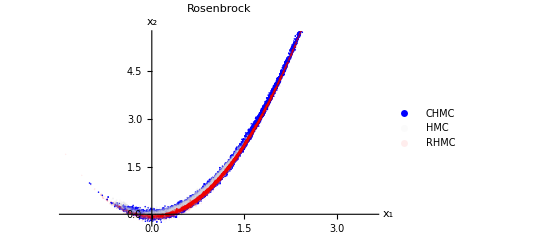

```mathematica
ListPlot[{QSchmc,QShmc,QSrhmc},PlotStyle->{Directive[Opacity[1],Blue],Directive[Opacity[.1],LightGray],Directive[Opacity[.07],Red]},PlotLegends->{Style["CHMC",Blue],Style["HMC",Gray],Style["RHMC",Red]},PlotLabel->Rosenbrock,AxesLabel->{"x_1","x_2"}]
```

10 chains trace

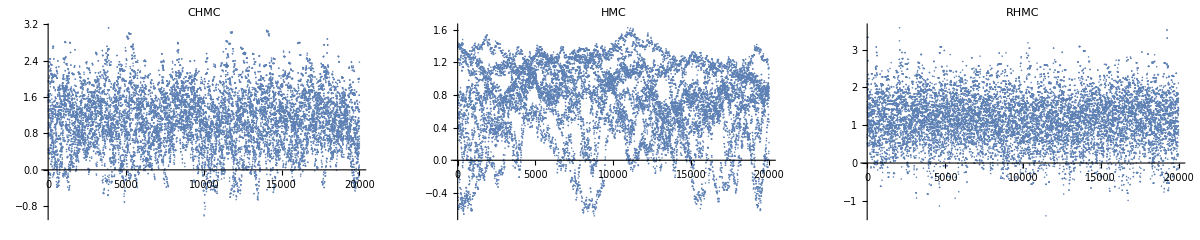

```mathematica
GraphicsRow[{ListPlot[QSchmc[[;;,1]],PlotLabel->"CHMC"],ListPlot[QShmc[[;;,1]],PlotLabel->"HMC"],ListPlot[QSrhmc[[;;,1]],PlotLabel->"RHMC"]}]
```